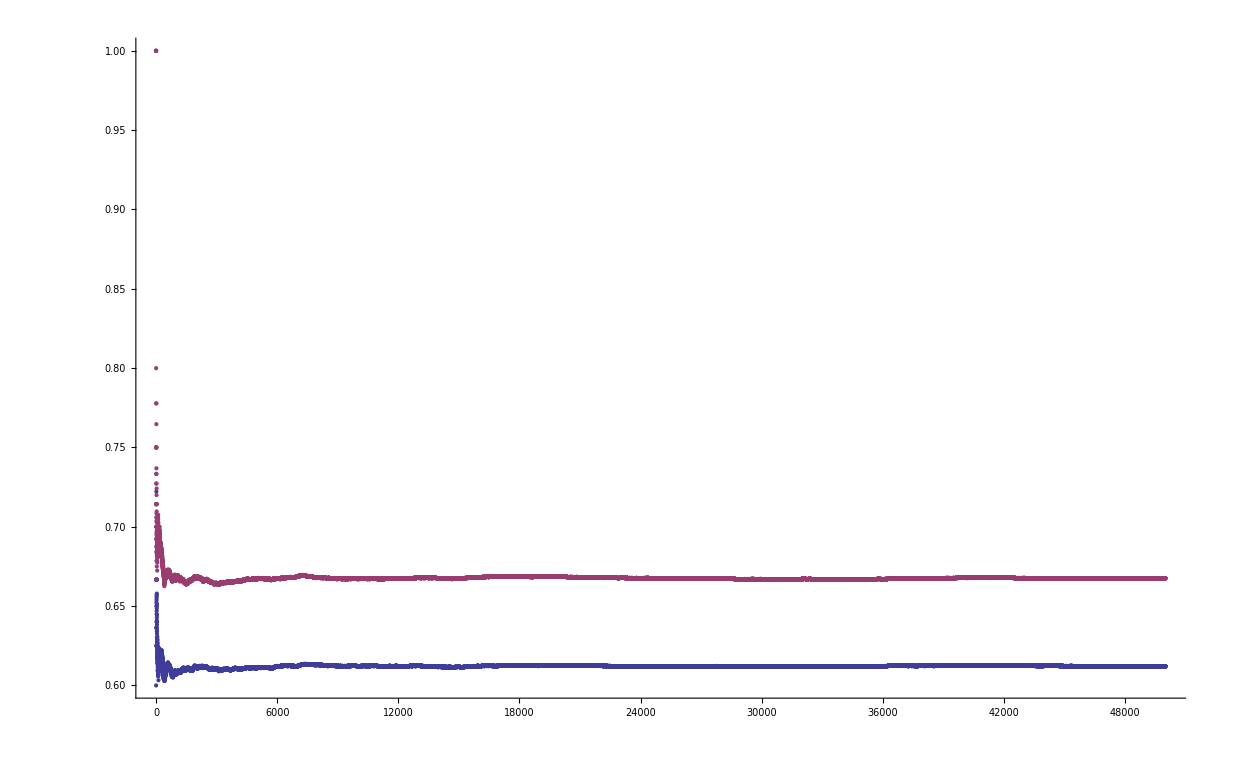

```mathematica
With[
 {tuple={3,5}, range=50000  },
With[
{voted=Monitor[ReadList[FileNameForVotedValues[tuple],Expression,range], "Reading"]}
,
ListPlot[
Monitor[
Table[
With[
{zeroes=Monitor[Map[If[Distance[#,p] == 0,1,0]&, voted], "Mapping " ]},
With[
{values=Monitor[Accumulate[zeroes ], "Accumulating"], LogP=1},
Monitor[
Table[N[values[[i]]/i]/LogP, {i,1,Length[values]}]
,i]
]
]
,{p, tuple}
]
, ToString[p] 
]
]
]
]
```

```mathematica
a=With[
 {range=500000  },
With[
{tupleRange=Sort[Select[ Map[#[[1]]&,ReadList[FileNameForVotedValuesSummary[range]]], magicGraham[#]>0  && Length[#]==4&]]},
Monitor[
Table[
With[
{voted=Monitor[ReadList[FileNameForVotedValues[tupleRange[[tuplePos]]],Expression,range], "Reading"]
}
,
Monitor[
Flatten[
Table[
With[
{zeroes=Monitor[Map[If[Distance[#,p] == 0,1,0]&, voted], "Mapping " ]},
With[
{values=Monitor[Accumulate[zeroes ], "Accumulating"]},
Monitor[
Table[{p,values[[i]]/i}, {i,Length[values],Length[values]}]
,i]
]
]
,{p, tupleRange[[tuplePos]]}
]
,1]
, ToString[p] 
]
],
{tuplePos,1,Length[tupleRange]}]
, ToString[tupleRange[[tuplePos]]] <> " --> " <> ToString[tuplePos] <> " / " <> ToString[Length[tupleRange]]
]
]
]
```

{{{3,171827/500000},{17,3899/15625},{23,23551/100000},{29,56633/250000}},{{3,176959/500000},{19,33473/125000},{23,4078/15625},{29,32089/125000}},{{5,161707/500000},{11,4441/15625},{17,66591/250000},{29,24769/100000}},{{5,157463/500000},{11,136547/500000},{19,123151/500000},{23,12023/50000}},{{5,16927/50000},{11,153581/500000},{19,72323/250000},{29,140171/500000}},{{5,179421/500000},{11,8439/25000},{23,19909/62500},{29,32339/100000}},{{5,81829/250000},{13,35249/125000},{17,67911/250000},{23,131227/500000}},{{5,5307/15625},{13,75127/250000},{19,36053/125000},{23,71423/250000}},{{5,18587/50000},{17,167909/500000},{19,85269/250000},{23,171233/500000}},{{7,142611/500000},{11,129427/500000},{13,125089/500000},{19,57687/250000}},{{7,19543/62500},{11,145393/500000},{13,143699/500000},{23,133481/500000}},{{7,163161/500000},{11,19401/62500},{17,18351/62500},{19,148101/500000}},{{7,43653/125000},{11,42011/125000},{17,81919/250000},{23,32627/100000}},{{7,180047/500000},{11,87791/250000},{19,85151/250000},{23,43187/125000}},{{7,87367/250000},{13,165711/500000},{17,80873/250000},{19,165179/500000}},{{7,46619/125000},{13,36207/100000},{17,89961/250000},{23,181121/500000}},{{7,192139/500000},{13,2359/6250},{19,187079/500000},{23,763/2000}},{{7,52209/125000},{17,206009/500000},{19,211191/500000},{23,54211/125000}},{{11,5177/12500},{13,207833/500000},{17,208937/500000},{19,107909/250000}},{{11,54359/125000},{13,219517/500000},{17,8899/20000},{23,229173/500000}},{{11,223219/500000},{13,113441/250000},{19,229713/500000},{23,2963/6250}},{{11,119649/250000},{17,239651/500000},{19,24609/50000},{23,63663/125000}},{{13,124169/250000},{17,125179/250000},{19,257279/500000},{23,266901/500000}}}

```mathematica
Map[Map[Plus,#]&,a]
```

{{{3,12237/20000},{5,16693/25000}},{{3,9927/25000},{5,19119/50000},{7,18443/50000}},{{5,68631/100000},{7,36177/50000}},{{3,30849/50000},{7,71209/100000}}}

```mathematica
Length[Select[ Map[#[[1]]&,ReadList[FileNameForVotedValuesSummary[500000]]], magicGraham[#]>0 && Length[#]==4&]]
```

23

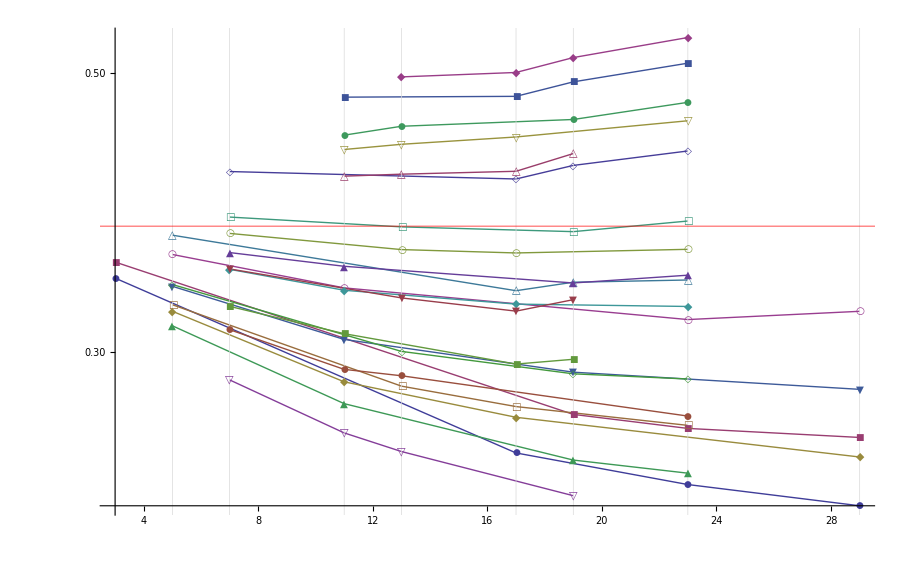

```mathematica
ListLogPlot[Select[a,Length[#]==4&], Joined->True,PlotMarkers->Automatic, GridLines->Automatic, PlotRange->{All,{0,1}}]
```

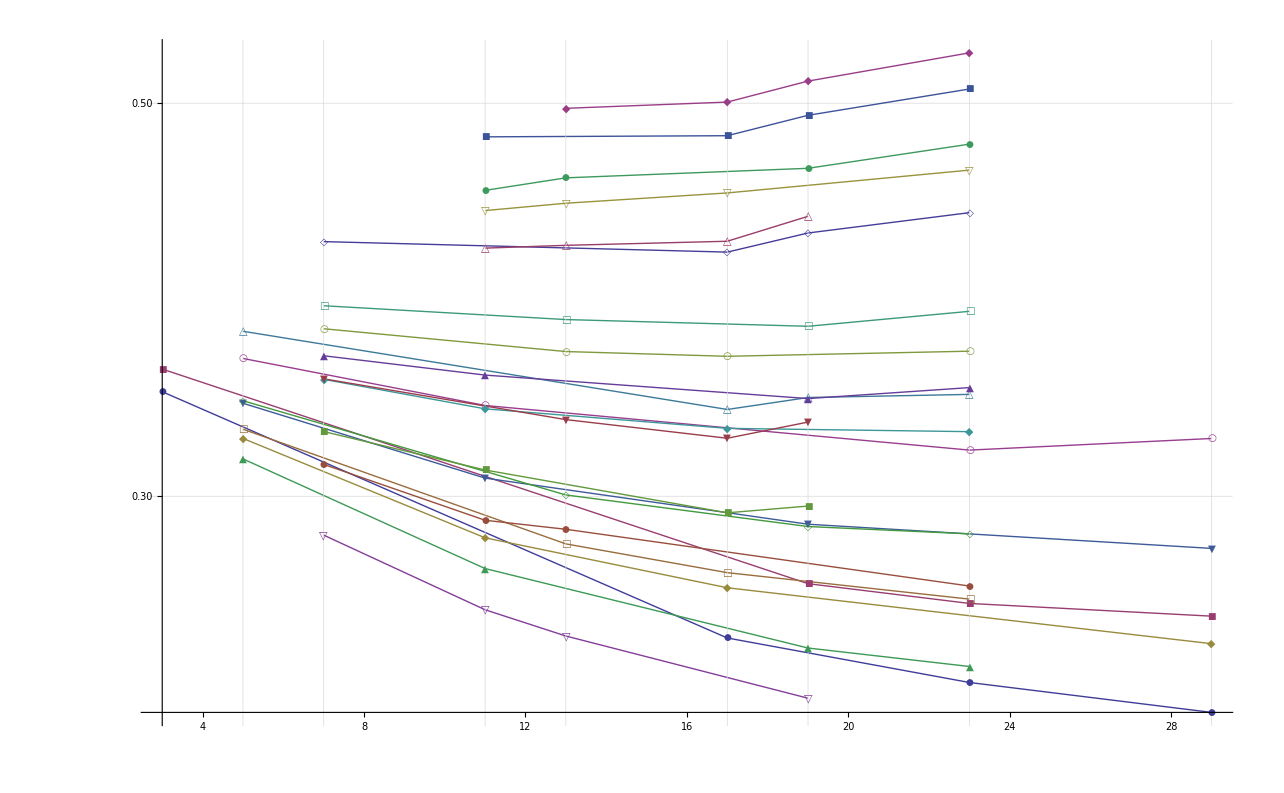

```mathematica
ListLogPlot[
Select[a,Length[#]==4&], 
Joined->True,
PlotMarkers->Automatic, 
GridLines->{Prime[Range[2,25]],
Range[0,1,0.02]}, 
PlotRange->{All,{0,1}}, 
PlotStyle->Thick]
```

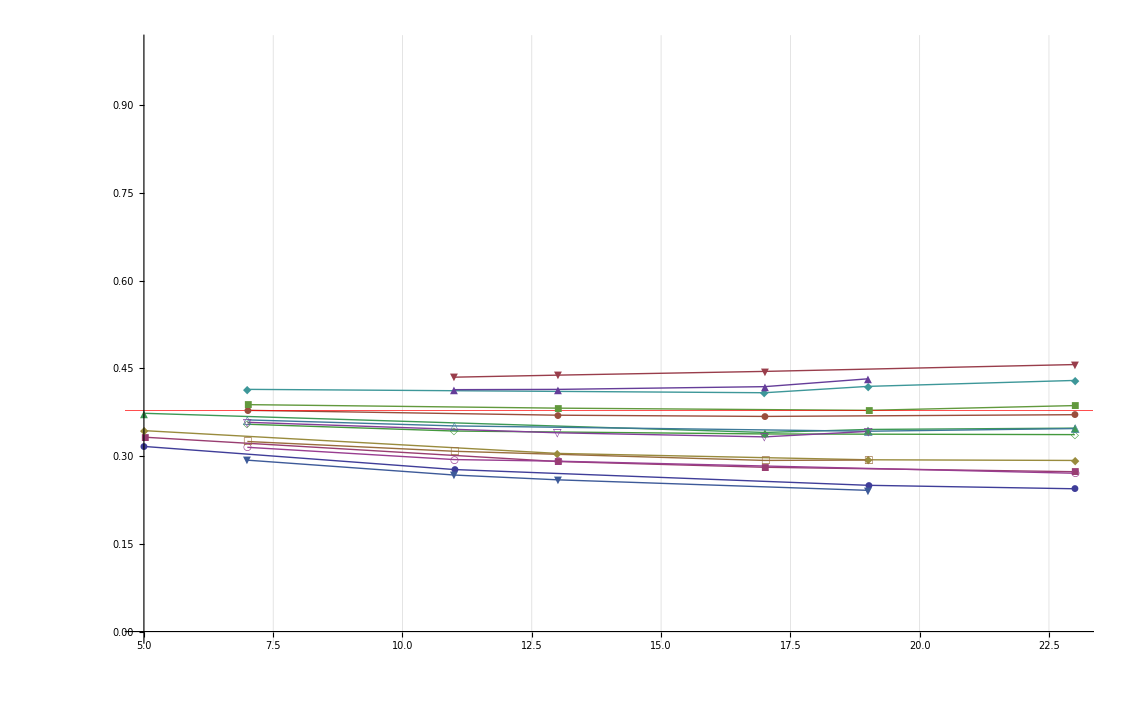

```mathematica
ListLinePlot[Select[a,Length[#]==4&], PlotMarkers->Automatic, GridLines->{Automatic,{{N[1/Sqrt[7]],Directive[Thick,Red]}}}, PlotRange->{All,{0,1}}]
```

```mathematica
N[1/E]
```

0.367879

```mathematica
With[
{summary = ReadList[FileNameForVotedValuesSummary[100000]]},
summary
]
```

{{{3,5},22890746207028},{{3,5,7},273435422080253278485945020132398792350078798892445329110699277051923190427},{{5,7},198343782038},{{3,7},986808051643},«160»,{{7,23},624606847},{{11,23},297860856},{{13,23},194307155},{{17,23},149523487}}